```mathematica
AdministrativeDivisionData[{"LosAngelesCounty", "California", "UnitedStates"}]
```

Los Angeles County, California, United States

```mathematica
EntityList@
FilteredEntityClass["University",
EntityFunction[e,
GeoWithinQ[Entity["AdministrativeDivision",{"LosAngelesCounty","California","UnitedStates"}],e]]]
```

$Aborted

```mathematica
GeoListPlot@
GeoEntities[Entity["AdministrativeDivision",{"LosAngelesCounty","California","UnitedStates"}],"City"]
```

-Graphics-

```mathematica
GeoListPlot@
GeoEntities[AdministrativeDivisionData[{"KernCounty", "California", "UnitedStates"}],"City"]
```

-Graphics-

```mathematica
Sum[RandomInteger[{0,9}] x^i,{i,0,6}]
```

7+2 x+4 x^2+x^3+6 x^4+5 x^5+7 x^6

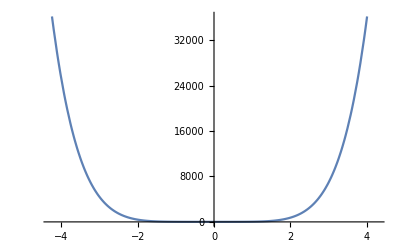

```mathematica
Plot[7+2 x+4 x^2+x^3+6 x^4+5 x^5+7 x^6,{x,-4.285714285714286,4.285714285714286}]
```

```mathematica
Plot[Sum[RandomInteger[{0,9}] x^i,{i,0,6},{x,-4.285714285714286,4.285714285714286}]
```

```mathematica
Plot[Sum[RandomInteger[{0,9}] x^i,{i,0,6},{x,-3,3}]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[∑_(i=0)^6 ∑_(x=-3)^3 RandomInteger[{0,9}] x^i]

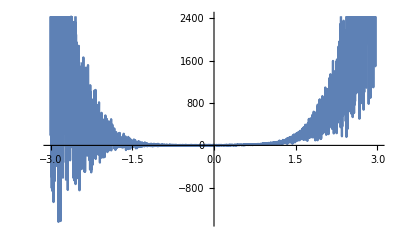

```mathematica
Plot[Sum[RandomInteger[{0,9}] x^i,{i,0,6}],{x,-3,3}]
```

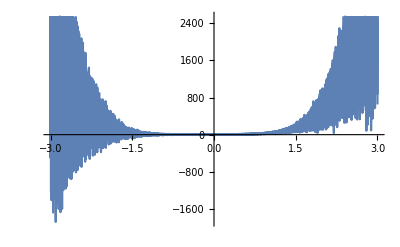

```mathematica
Plot[Table[Sum[RandomInteger[{0,9}] x^i,{i,0,6}],{n,1,5}],{x,-3,3}]
```

```mathematica
Plot[
Table[
Sum[RandomInteger[{0,9}] x^i,{i,0,6}]
,{n,1,5}],
{x,-3,3},
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/2,ImageSize->Full
]
```

-Graphics-

```mathematica
Plot[
Table[
Sum[RandomInteger[{0,9}] x^i,{i,0,6}]
,{n,1,5}],
{x,-3,3},
PlotTheme->"Marketing",PlotLegends->"Expressions",AspectRatio->1/2,ImageSize->Full
]
```

-Graphics-

```mathematica
Plot[
Table[
Sum[RandomInteger[{0,9}] x^i,{i,0,6}]
,{n,1,5}],
{x,-2,2},
PlotTheme->"Marketing",PlotLegends->"Expressions",AspectRatio->1/2,ImageSize->Full
]
```

-Graphics-

```mathematica
Plot[
Table[
Sum[RandomInteger[{0,9}] x^i,{i,0,6}]
,{n,1,5}],
{x,-2,2},
PlotTheme->"Marketing",PlotLegends->"Expressions",AspectRatio->1/2,ImageSize->Full
]
```

-Graphics-

```mathematica
Plot[
Table[
Sum[RandomInteger[{0,9}] x^i,{i,0,6}]
,{n,1,5}],
{x,-1,1},
PlotTheme->"Marketing",PlotLegends->"Expressions",AspectRatio->1/2,ImageSize->Full
]
```

-Graphics-

```mathematica
Sum[RandomInteger[{0,9}] x^i,{i,0,6}]
```

2+9 x+5 x^2+5 x^4+3 x^5+8 x^6

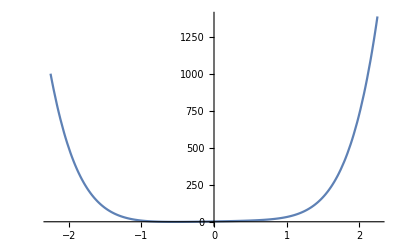

```mathematica
Plot[2+9 x+5 x^2+5 x^4+3 x^5+8 x^6,{x,-2.25,2.25}]
```

```mathematica
Sum[RandomInteger[{0,9}] x^i,{i,0,6}]
```

7+6 x+x^2+7 x^3+6 x^5+5 x^6

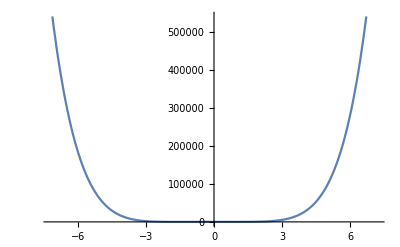

```mathematica
Plot[7+6 x+x^2+7 x^3+6 x^5+5 x^6,{x,-7.199999999999999,7.199999999999999}]
```

```mathematica
2+9 x+5 x^2+5 x^4+3 x^5+8 x^6
```

2+9 x+5 x^2+5 x^4+3 x^5+8 x^6

```mathematica
Plot[2+9 x+5 x^2+5 x^4+3 x^5+8 x^6,{x,-2.25,2.25}]
```

-Graphics-

```mathematica
FullSimplify[ArcCurvature[{x,2+9 x+5 x^2+5 x^4+3 x^5+8 x^6},x],x∈Reals]
```

(10+60 x^2 (1+x+4 x^2))/((82+x (10+x^2 (20+3 x (5+16 x))) (18+10 x+x^3 (20+3 x (5+16 x))))^(3/2))

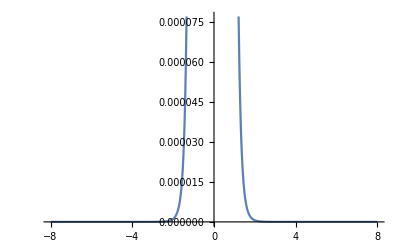

```mathematica
Plot[(10+60 x^2 (1+x+4 x^2))/((82+x (10+x^2 (20+3 x (5+16 x))) (18+10 x+x^3 (20+3 x (5+16 x))))^(3/2)),{x,-8,8}]
```

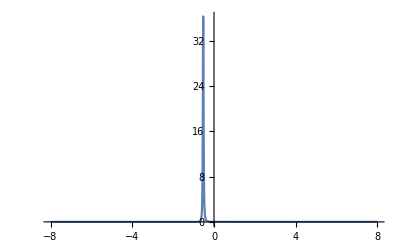

```mathematica
Plot[(10+60 x^2 (1+x+4 x^2))/((82+x (10+x^2 (20+3 x (5+16 x))) (18+10 x+x^3 (20+3 x (5+16 x))))^(3/2)),{x,-8,8},PlotRange->Full]
```

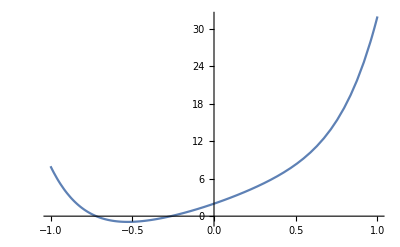

```mathematica
Plot[2+9 x+5 x^2+5 x^4+3 x^5+8 x^6,{x,-1,1}]
```

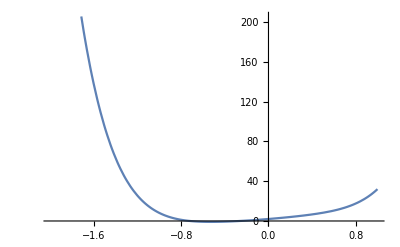

```mathematica
Plot[2+9 x+5 x^2+5 x^4+3 x^5+8 x^6,{x,-2,1}]
```

```mathematica
FullSimplify[ArcCurvature[{x,α x^2+β x},x],{α,β,x}∈Reals]
```

(2 Abs[α])/((1+(2 x α+β)^2)^(3/2))

```mathematica
Manipulate[Plot[(2 Abs[α])/((1+(2 x α+β)^2)^(3/2)),{x,-1.2984547082626388,1.2984547082626388}],{α,-1.2984547082626388,1.2984547082626388},{β,-2,2}]
```

```mathematica
(2 Abs[α])/((1+(2 x α+β)^2)^(3/2))/.β->0
```

(2 Abs[α])/((1+4 x^2 α^2)^(3/2))

```mathematica
Manipulate[Plot[(2 Abs[α])/((1+4 x^2 α^2)^(3/2)),{x,-2.5067500167481853,2.5067500167481853}],{α,-2.5067500167481853,2.5067500167481853}]
```

```mathematica
Plot3D[
(2 Abs[α])/((1+4 x^2 α^2)^(3/2)),
{x,-10,10},{α,-3,3}
]
```

-Graphics3D-

```mathematica
Plot3D[
(2 Abs[α])/((1+4 x^2 α^2)^(3/2)),
{x,-10,10},{α,-3,3}
,PlotRange->Full
]
```

-Graphics3D-

```mathematica
Grad[(2 Abs[α])/((1+4 x^2 α^2)^(3/2)),{x,α}]
```

{-(24 x α^2 Abs[α])/((1+4 x^2 α^2)^(5/2)),-(24 x^2 α Abs[α])/((1+4 x^2 α^2)^(5/2))+(2 Abs'[α])/((1+4 x^2 α^2)^(3/2))}

```mathematica
Solve[{-(24 x α^2 Abs[α])/((1+4 x^2 α^2)^(5/2))==0,-(24 x^2 α Abs[α])/((1+4 x^2 α^2)^(5/2))+(2 Abs'[α])/((1+4 x^2 α^2)^(3/2))==0},{x,α}]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -α == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→0,α→InverseFunction[Abs',1,1][0]}}

```mathematica
CountryData[]
```

{Afghanistan,Aland Islands,Albania,Algeria,American Samoa,Andorra,Angola,Anguilla,Antigua and Barbuda,Argentina,Armenia,Aruba,Australia,Austria,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bermuda,Bhutan,Bolivia,Caribbean Netherlands,Bosnia and Herzegovina,Botswana,Bouvet Island,Brazil,British Indian Ocean Territory,British Virgin Islands,Brunei,Bulgaria,Burkina Faso,Burundi,Cambodia,Cameroon,Canada,Cape Verde,Cayman Islands,Central African Republic,Chad,Chile,China,Christmas Island,Cocos Keeling Islands,Colombia,Comoros,Cook Islands,Costa Rica,Croatia,Cuba,Curacao,Cyprus,Czech Republic,Democratic Republic of the Congo,Denmark,Djibouti,Dominica,Dominican Republic,East Timor,Ecuador,Egypt,El Salvador,Equatorial Guinea,Eritrea,Estonia,Ethiopia,Falkland Islands,Faroe Islands,Fiji,Finland,France,French Guiana,French Polynesia,French Southern And Antarctic lands,Gabon,Gambia,Gaza Strip,Georgia,Germany,Ghana,Gibraltar,Greece,Greenland,Grenada,Guadeloupe,Guam,Guatemala,Guernsey,Guinea,Guinea-Bissau,Guyana,Haiti,Honduras,Hong Kong,Hungary,Iceland,India,Indonesia,Iran,Iraq,Ireland,Isle of Man,Israel,Italy,Ivory Coast,Jamaica,Japan,Jersey,Jordan,Kazakhstan,Kenya,Kiribati,Kosovo,Kuwait,Kyrgyzstan,Laos,Latvia,Lebanon,Lesotho,Liberia,Libya,Liechtenstein,Lithuania,Luxembourg,Macau,North Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Malta,Marshall Islands,Martinique,Mauritania,Mauritius,Mayotte,Mexico,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Montserrat,Morocco,Mozambique,Myanmar,Namibia,Nauru,Nepal,Netherlands,New Caledonia,New Zealand,Nicaragua,Niger,Nigeria,Niue,Norfolk Island,Northern Mariana Islands,North Korea,Norway,Oman,Pakistan,Palau,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Pitcairn Islands,Poland,Portugal,Puerto Rico,Qatar,Republic of the Congo,Réunion,Romania,Russia,Rwanda,Saint Barthelemy,Saint Helena, Ascension and Tristan da Cunha,Saint Kitts and Nevis,Saint Lucia,Saint Martin,Saint Pierre and Miquelon,Saint Vincent and the Grenadines,Samoa,San Marino,São Tomé and Príncipe,Saudi Arabia,Senegal,Serbia,Seychelles,Sierra Leone,Singapore,Sint Maarten,Slovakia,Slovenia,Solomon Islands,Somalia,South Africa,South Georgia and the South Sandwich Islands,South Korea,South Sudan,Spain,Sri Lanka,Sudan,Suriname,Svalbard,Eswatini,Sweden,Switzerland,Syria,Taiwan,Tajikistan,Tanzania,Thailand,Togo,Tokelau,Tonga,Trinidad and Tobago,Tunisia,Turkey,Turkmenistan,Turks and Caicos Islands,Tuvalu,Uganda,Ukraine,United Arab Emirates,United Kingdom,United States,United States Minor Outlying Islands,United States Virgin Islands,Uruguay,Uzbekistan,Vanuatu,Vatican City,Venezuela,Vietnam,Wallis and Futuna Islands,West Bank,Western Sahara,Yemen,Zambia,Zimbabwe}

```mathematica
EntityClass["Country",All]
```

countries

```mathematica
"plot in world map""country group"Manipulate[Graphics[({If[CountryData[#1,cl],Directive[Orange,EdgeForm[Brown]],LightBrown],Tooltip[CountryData[#1,{"SchematicPolygon","Robinson"}],{CountryData[#1,"Name"],CountryData[#1,prop]}]}&)/@CanonicalName[CountryData[]],ImageSize->500],{{cl,All,"country group"},Dynamic[CanonicalName[CountryData["Classes"]],SynchronousUpdating->False],ControlType->PopupMenu},{{prop,"Population","country property"},Dynamic[CountryData["Properties"],SynchronousUpdating->False],ControlType->PopupMenu},SynchronousUpdating->False]
```

CountryData::notprop: All is not a known property for CountryData. Use CountryData["Properties"] for a list of properties.

General::stop: Further output of CountryData::notprop will be suppressed during this calculation.

```mathematica
Total@EntityClass["Country",All]["Population"]
```

Missing[NotAvailable]+7552596367 people

```mathematica
Total@EntityClass["Country",All]["GDP"]
```

17 Missing[NotAvailable]+8.55135×10^13 $

```mathematica
EntityProperties["Country"]
```